814

Export::errfile: The file E:\Users\Almanzor\Documents\Escuela\Biomecanica\Practicas\TvsAngR.xls (Acceso denegado) could not be accessed.

101

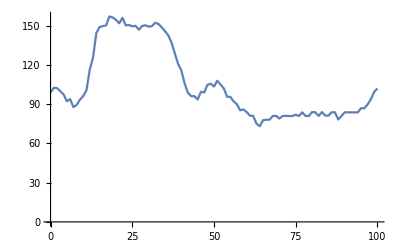

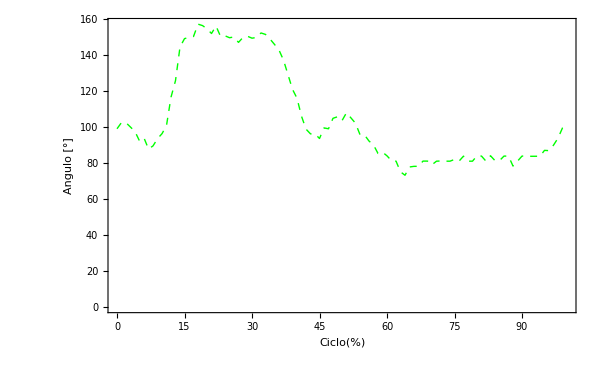

```mathematica
(*Importamos el archivo excel con los datos biomecanicos *)
e=Import["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Practicas\\Ciclo Ataque105.xls"][[3]];
VMx= e[[1,6]]-e[[1,4]];
VMy = e[[1,7]]-e[[1,5]];
long = Length[e]
VB = Table[{e[[i,6]]-e[[i,4]],e[[i,7]]-e[[i,5]]},{i,1,long}];
VA = Table[{e[[i,2]]-e[[i,4]],e[[i,3]]-e[[i,5]]},{i,1,long}];
MoVA = Table[{Norm[VA[[i]]]},{i,1,long}];
MoVB = Table[{Norm[VB[[i]]]},{i,1,long}];
Propunt = Table[{VA[[i]].VB[[i]]},{i,1,long}];
AngR = Table[{ArcCos[(Propunt[[i,1]])/(MoVA[[i,1]]*MoVB[[i,1]])]/Degree},{i,1,long}];
TvsAngR = Table[{(e[[i,1]]-e[[1,1]]),AngR[[i,1]]},{i,1,long}];
Export["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Practicas\\TvsAngR.xls",TvsAngR];
ListPlot[TvsAngR];
inc1 = (e[[long,1]]-e[[1,1]])/100;
PTvsA = Interpolation[TvsAngR,InterpolationOrder->1];
ParaPTvsA = Table[{(i/inc1),PTvsA[i]},{i,TvsAngR[[1,1]],TvsAngR[[long,1]],inc1}];
Length[ParaPTvsA]
ListPlot[{ParaPTvsA},Joined->True]
Ciclo = ListPlot[Tooltip[{ParaPTvsA}],Joined->True,PlotStyle->{{Green,Dashed,Thick}},Frame->True,FrameLabel->{{"Angulo [°]","Mean+/- SD"},{"Ciclo(%)","Ang vs Ciclo"}},BaseStyle->{12,FontFamily->"Arial"},ImageSize->600]
```